```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]<>"/Data"]
<<DISY`
```

/home/roma/Yandex.Disk/Programming/DISY/Data

Hello, I am DISY. Hopefully I can help you, with the reduction of the differential systems to ϵ-form.

To start with, please, define the differential system.
    See ?NewDSystem for details.

TODO list:

• clean extra, consolidate history

• rewrite JDecomposition and JFormQ: should preserve block-triangular structure is possible.

• NB: Series redefined!

• improve A0A1ToSubspaces — calculate Groebner basis of u_1(λ),…,u_k(λ).

```mathematica
FileNames[]
```

{BT122,BT122transformation,Example1,Example6x6,ff3lm1051-Amatrixs.m,Ms,Mt}

```mathematica
Quit
```

```mathematica
Get["Ms"]//Length
```

Differential system in s.

75

```mathematica
2+2
```

4

```mathematica
NewDSystem[ds,Factor[{s->Get["Ms"],t->Get["Mt"]}/.{mm->1,d->4-2ϵ}]]
```

Differential system in s.

Differential system in t.

NewDEsystem[ds,{s→{1},t→{1}}]
 |  |  |  |

```mathematica
Factor[Denominators[ds]/.s->2-t-u]
```

Added extra(s) Denominators to current history entry.

{-2-t-u,2-t-u,-2+t,-1+t,t,1+t,-1-u,-u,1-u,2-u,1-t u,-1+2 ϵ+t ϵ-u ϵ}

Very natural letters

```mathematica
?DISY`*
```

HalfProjectors[
StyleBox["A0", "TI"],
StyleBox["A1", "TI"],Left|Right] gives the subspaces which may be used for the construction of the projectors for the balances.

```mathematica
SeriesCoefficient
```

```mathematica
HalfProjectors[]
```

```mathematica
Quit
```

## Retrieving data

Getting the number of equations

```mathematica
Length[ds]
```

0

Getting original Association list:

```mathematica
ds[[]]
```

<|s→{1},t→{1}|>
 |  |  |  |

Getting specific matrices:

```mathematica
ds[s]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},74}
 |  |  |  |

```mathematica
ds[t]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},74}
 |  |  |  |

block structure:

```mathematica
EntangledBlocksIndices[ds]
```

Added extra(s) TClosure to current history entry.

{{1},{2},{3},{4},{5},{6},{7},{8},{9,10},{11},{12,13,14},{15},{16},{17},{18},{19},{20,21},{22},{23},{24},{25},{26},{27},{28},{29},{30,31},{32,33},{34,35},{36,37},{38,39},{40},{41},{42},{43},{44},{45,46},{47,48},{49},{50},{51},{52,53,54,55},{56},{57},{58},{59,60,61,62},{63},{64},{65},{66},{67},{68,69},{70,71,72},{73,74,75}}

Getting parts:

```mathematica
ds[[{20,21},{20,21}]]
```

<|s→{{-(-4+s+t+16 ϵ-6 s ϵ-6 t ϵ-14 ϵ^2+6 s ϵ^2+6 t ϵ^2)/((-2+s+t) (-1+s+t) (-3+4 ϵ)),(2 (-1+ϵ) (-2+3 ϵ))/((-2+s+t) (-1+s+t) (-3+4 ϵ))},{-((-1+s+t) (-1+ϵ) (-1+2 ϵ))/((-2+s+t) (-3+4 ϵ)),((-1+2 ϵ) (4-s-t-5 ϵ+s ϵ+t ϵ))/((-2+s+t) (-1+s+t) (-3+4 ϵ))}},t→{{-(-4+s+t+16 ϵ-6 s ϵ-6 t ϵ-14 ϵ^2+6 s ϵ^2+6 t ϵ^2)/((-2+s+t) (-1+s+t) (-3+4 ϵ)),(2 (-1+ϵ) (-2+3 ϵ))/((-2+s+t) (-1+s+t) (-3+4 ϵ))},{-((-1+s+t) (-1+ϵ) (-1+2 ϵ))/((-2+s+t) (-3+4 ϵ)),((-1+2 ϵ) (4-s-t-5 ϵ+s ϵ+t ϵ))/((-2+s+t) (-1+s+t) (-3+4 ϵ))}}|>

Combined (first goes part specification, then argument):

```mathematica
ds[[{20,21},{20,21}]][s]
```

{{-(-4+s+t+16 ϵ-6 s ϵ-6 t ϵ-14 ϵ^2+6 s ϵ^2+6 t ϵ^2)/((-2+s+t) (-1+s+t) (-3+4 ϵ)),(2 (-1+ϵ) (-2+3 ϵ))/((-2+s+t) (-1+s+t) (-3+4 ϵ))},{-((-1+s+t) (-1+ϵ) (-1+2 ϵ))/((-2+s+t) (-3+4 ϵ)),((-1+2 ϵ) (4-s-t-5 ϵ+s ϵ+t ϵ))/((-2+s+t) (-1+s+t) (-3+4 ϵ))}}

## Operations

```mathematica
Apart[ds]
```

History length for ds is 2.

<|s→{1},t→{1}|>
 |  |  |  |

## Boilerplate

#### Visual interface

Хорошо бы сразу написать вот такой интерфейс:
Есть набор кнопок, каждая может быть нажата или не нажата. Некоторые комбинации запрещены. 
Запрещены они могут быть по-разному: 
при попытке перехода в одни интерфейс сбрасывается, а в другие --- ничего не происходит.

```mathematica
?JordanDecomposition
```

RowBox[{"JordanDecomposition", "[", StyleBox["m", "TI"], "]"}] yields the Jordan decomposition of a square matrix StyleBox["m", "TI"]. The result is a list RowBox[{"{", RowBox[{StyleBox["s", "TI"], ",", StyleBox["j", "TI"]}], "}"}] where StyleBox["s", "TI"] is a similarity matrix and StyleBox["j", "TI"] is the Jordan canonical form of StyleBox["m", "TI"].

```mathematica
{#1,#2,{},{},JDecompositionData[#3]}&@@@({#1,#2,LeadingPoleCoefficient[m,{x,#1}]}&@@@PolesInfo[m,x])
```

```mathematica
EntangledBlocksIndices[ds]
```

Added extra(s) TClosure to current history entry.

{{1},{2},{3},{4,5,6},{7},{8,9,10,11},{12},{13},{14},{15},{16,17,18},{19,20},{21,22},{23,24},{25,26},{27},{28,29}}

```mathematica
ds[s][[{8,9,10,11},{8,9,10,11}]]
```

{{(-2+5 ep)/((-4+s) s),-(-6+11 ep+ep s)/(2 (-1+2 ep) (-4+s) s),(ep (-1+3 ep))/(2 (-1+2 ep)^2),-(6-23 ep+22 ep^2-3 ep s+7 ep^2 s)/(2 (-1+2 ep)^2 (-4+s) s)},{-(2 (-1+2 ep) (-1+3 ep) (-3+s))/((-4+s) s),(5-11 ep-2 s+5 ep s)/((-4+s) s),-(ep (-1+3 ep))/(-1+2 ep),((-1+3 ep) (5-10 ep-2 s+5 ep s))/((-1+2 ep) (-4+s) s)},{-(4 (-1+2 ep)^2)/((-4+s) s),(3 (-1+2 ep))/((-4+s) s),-(-2-4 ep+5 ep s)/((-4+s) s),(-3+7 ep)/((-4+s) s)},{(2 (-1+2 ep)^2)/((-4+s) s),-(3 (-1+2 ep))/((-4+s) s),0,-(-3+2 ep+2 ep s)/((-4+s) s)}}

```mathematica
VisBalancing[ds[s][[{4,5,6},{4,5,6}]],s]
```

$Failed

```mathematica
makePalette[labels_List]:=Module[{state,buttons,request,toggle},
state=Replace[labels,l_:>{l,Unique[]},{2}];
buttons=MapIndexed[(Function[{label,var},If[label=!=Null,Button[label,request@#2,Appearance->If[Dynamic[var],{"Palette","Pressed"},{"Palette"}]],Null]]@@#)&,state,{2}];
(*state is the state of the buttons, buttons*)
state=Map[Hold,state[[All,All,2]],{2}];
Apply[(#=False)&,state,{2}];
SetAttributes[toggle,HoldAll];
toggle[x_]:=x=Not[x];
request=If[True(*here goes validation, depending on position #={i,j}*),MapAt[ReleaseHold[toggle/@#]&,state,#]]&;
Grid[buttons,Spacings->{0,0}]
]
```

```mathematica
labels={{"a","b","f"},{"c","d",Null,"g"}};
makePalette[labels]
```

a | b | f | 
c | d |  | g

```mathematica
x=.
```

```mathematica
Factor[Inverse[{{1,1/x},{0,1}}].D[{{1,1/x},{0,1}},x]]
```

{{0,-1/x^2},{0,0}}

```mathematica
x=False;Button["label",x=Not[x],Appearance->If[Dynamic[x],{"DialogBox","Pressed"},{"DialogBox"}]]
```

label

```mathematica
x=
```

0

```mathematica
PaletteNotebook
```

```mathematica
ButtonBar[{"a":>Print[1],"b":>Print[2]}]
```

a | b

```mathematica
Button["xxx",Null,Appearance->{a,"Pressed"}]
```

```mathematica
Quit
```

```mathematica
?ds
```

Differential system for 75 functions of s,t.

```mathematica
Eigen
```

```mathematica
JordanDecomposition
```

Visual interface:

```mathematica
DISYPallete[]
```

```mathematica
ButtonBar
```

```mathematica
DialogInput[Button["OK",DialogReturn["Success"]]]
```

Success

```mathematica
DialogInput[Button["OK",DialogReturn["Success"]]]
```

```mathematica
CreateDialog[{Checkbox[Dynamic[x]],Checkbox[Dynamic[y]],Checkbox[Dynamic[z],Enabled->Dynamic[x&&y]],DefaultButton[]}]
```

5rkb4_shm76FrontEndObject[LinkObject["5rkb4_shm", 3, 1]]7676

```mathematica
PaletteNotebook
```

```mathematica
Needs["GUIKit`"]
ref=GUIRun["Wolfram/Example/Calculator"]
```

⁃GUIObject⁃

#### Matrix operations

```mathematica
Quit
```

```mathematica
Context[LeadingSeries]
```

DISY`

```mathematica
LeadingSeries[ds[s],{s,4,2}]
```

{{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],O[s-4]^0,1/O[s-4],O[s-4]^0,1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],O[s-4]^0,1/O[s-4],O[s-4]^0,1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],((-2+3 ep) (-3+4 ep))/((-1+2 ep) (s-4)^2)+1/O[s-4],(5 ep)/((-1+2 ep) (s-4)^2)+1/O[s-4],-(3 (-2+3 ep))/((-1+2 ep) (s-4)^2)+1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],(-87/2+9/ep+69 ep-36 ep^2)/(s-4)^2+1/O[s-4],(15/2-15 ep)/(s-4)^2+1/O[s-4],(-63/2+9/ep+27 ep)/(s-4)^2+1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],O[s-4]^0,1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],((-1+ep) (-2+3 ep) (-1+3 ep))/(8 (-1+6 ep) (s-4)^2)+1/O[s-4],((-2+3 ep) (-3+4 ep) (1-8 ep+5 ep^2))/(24 ep (-1+6 ep) (s-4)^2)+1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],((-1+2 ep)^2 (-1+7 ep))/(2 (-1+6 ep) (s-4)^2)+1/O[s-4],-(3 (ep (-1+2 ep)))/(2 (-1+6 ep) (s-4)^2)+1/O[s-4],(1-13 ep+40 ep^2)/(2 (-1+6 ep) (s-4)^2)+1/O[s-4],(3 ep-5 ep^2)/(4 (-1+6 ep) (s-4)^2)+1/O[s-4],1/O[s-4],((-1+2 ep)^2 (-2+3 ep))/(2 ep (s-4)^2)+1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],-((-2+3 ep) (-3+4 ep) (-3+10 ep))/((-1+3 ep) (-1+4 ep) (s-4)^2)+1/O[s-4],-(5 (ep (-3+10 ep)))/(((-1+3 ep) (-1+4 ep)) (s-4)^2)+1/O[s-4],(3 (-2+3 ep) (-3+10 ep))/((-1+3 ep) (-1+4 ep) (s-4)^2)+1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],O[s-4]^0,1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],(29/12-1/(2 ep)-(23 ep)/6+2 ep^2)/(s-4)^2+1/O[s-4],((-1+2 ep) (-2+3 ep) (-3+4 ep) (-3+10 ep))/(ep (-1+6 ep) (s-4)^3)+((-1+2 ep) (-2+3 ep) (-3+4 ep) (-5+16 ep))/(4 (-1+4 ep) (-1+6 ep) (s-4)^2)+1/O[s-4],(5 (-1+2 ep) (-3+10 ep))/((-1+6 ep) (s-4)^3)+((-1+2 ep) (48-414 ep+828 ep^2))/(12 (-1+4 ep) (-1+6 ep) (s-4)^2)+1/O[s-4],-(3 ((-1+2 ep) (-2+3 ep) (-3+10 ep)))/((ep (-1+6 ep)) (s-4)^3)-((-1+2 ep) (-2+3 ep) (-4+13 ep))/((-1+4 ep) (-1+6 ep) (s-4)^2)+1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],(11/2-1/ep-10 ep+6 ep^2)/(s-4)^2+1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],(-2+5 ep-3 ep^2)/(2 ep (s-4)^2)+1/O[s-4],1/O[s-4],-(2 (-6+41 ep-80 ep^2+48 ep^3))/((ep (-1+3 ep)) (s-4)^3)+(6-29 ep+46 ep^2-24 ep^3)/(4 ep (-1+3 ep) (s-4)^2)+1/O[s-4],-(10 (-1+4 ep))/((-1+3 ep) (s-4)^3)+(7-23 ep)/(2 (-1+3 ep) (s-4)^2)+1/O[s-4],(6 (2-11 ep+12 ep^2))/(ep (-1+3 ep) (s-4)^3)+(4-16 ep+15 ep^2)/(2 ep (-1+3 ep) (s-4)^2)+1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],(1-8 ep+20 ep^2-16 ep^3)/(ep (-1+3 ep) (s-4)^2)+1/O[s-4],(1-4 ep)/((-1+3 ep) (s-4)^2)+1/O[s-4],(2-13 ep+20 ep^2)/(ep (-1+3 ep) (s-4)^2)+1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],((-1+ep) (-1+2 ep) (-2+3 ep) (-1+3 ep) (-1+6 ep))/(8 ep^2 (-1+4 ep) (s-4)^2)+1/O[s-4],1/O[s-4],((-1+2 ep) (-2+3 ep) (-3+4 ep) (-7+34 ep))/(8 ep^2 (s-4)^3)-((-1+2 ep) (-2+3 ep) (-3+4 ep) (3-31 ep+72 ep^2))/(32 (ep^2 (-1+4 ep)) (s-4)^2)+1/O[s-4],(5 (7-48 ep+68 ep^2))/(8 ep (s-4)^3)+(-19+176 ep-544 ep^2+536 ep^3)/(32 ep (-1+4 ep) (s-4)^2)+1/O[s-4],-(3 ((-1+2 ep) (-2+3 ep) (-7+34 ep)))/(8 ep^2 (s-4)^3)+((-1+2 ep) (-2+3 ep) (7-72 ep+164 ep^2))/(32 ep^2 (-1+4 ep) (s-4)^2)+1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],(12+1/(4 ep^2)-3/ep-20 ep+12 ep^2)/(s-4)^2+1/O[s-4],(-2+1/(4 ep)+3 ep)/(s-4)^2+1/O[s-4],(16+1/(2 ep^2)-21/(4 ep)-15 ep)/(s-4)^2+1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],O[s-4]^0,1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],O[s-4]^0,1/O[s-4],O[s-4]^0,1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],O[s-4]^0,1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]},{1/O[s-4],-((-1+ep) (-2+3 ep) (-1+3 ep))/(4 (ep (-1+4 ep)) (s-4)^2)+1/O[s-4],1/O[s-4],-((-2+3 ep) (-3+4 ep) (3+14 ep))/(24 ep^2 (s-4)^3)-((-2+3 ep) (-3+4 ep) (-1+69 ep-698 ep^2+1728 ep^3))/(96 (ep^2 (-1+4 ep) (-1+6 ep)) (s-4)^2)+1/O[s-4],-(5 (3+14 ep))/(24 ep (s-4)^3)+(-11-244 ep+3696 ep^2-10056 ep^3)/(96 ep (-1+4 ep) (-1+6 ep) (s-4)^2)+1/O[s-4],((-2+3 ep) (3+14 ep))/(8 ep^2 (s-4)^3)+((-2+3 ep) (-3+218 ep-2204 ep^2+5448 ep^3))/(96 ep^2 (-1+4 ep) (-1+6 ep) (s-4)^2)+1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],O[s-4]^0,1/O[s-4],(2-1/(2 ep)-2 ep)/(s-4)^2+1/O[s-4],-1/(2 (s-4)^2)+1/O[s-4],(5/2-1/ep)/(s-4)^2+1/O[s-4],O[s-4]^0,O[s-4]^0,1/O[s-4],O[s-4]^0,1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],O[s-4]^0,1/O[s-4],1/O[s-4]},{1/O[s-4],((244-1420 ep) (-1+ep) (-1+2 ep) (-2+3 ep) (-1+3 ep))/(192 ep (-1+4 ep) (-1+6 ep) (s-4)^2)+1/O[s-4],((-1+2 ep) (-2+3 ep) (-3+4 ep) (-1+4 ep))/(12 ep^2 (s-4)^3)-((-1+2 ep) (-2+3 ep) (-3+4 ep) (-8+123 ep-579 ep^2+779 ep^3))/(144 (ep^2 (-1+4 ep) (-1+6 ep)) (s-4)^2)+1/O[s-4],(-18+327 ep-1898 ep^2+4812 ep^3-5560 ep^4+2400 ep^5)/(24 ep^3 (s-4)^4)+(-12+220 ep-2699 ep^2+22418 ep^3-74140 ep^4+101688 ep^5-49248 ep^6)/(96 ep^3 (-1+6 ep) (s-4)^3)+(6-101 ep+394 ep^2-3312 ep^3+13512 ep^4-20976 ep^5+10944 ep^6)/(384 ep^3 (-1+6 ep) (s-4)^2)+1/O[s-4],(5 (-3+46 ep-180 ep^2+200 ep^3))/(24 ep^2 (s-4)^4)+(3-91 ep+282 ep^2+3436 ep^3-7320 ep^4)/(48 ep^2 (-1+6 ep) (s-4)^3)+(-3+64 ep-1272 ep^2+8960 ep^3-13296 ep^4)/(384 ep^2 (-1+6 ep) (s-4)^2)+1/O[s-4],(-6+101 ep-498 ep^2+940 ep^3-600 ep^4)/(8 ep^3 (s-4)^4)+(-6+101 ep-1194 ep^2+9472 ep^3-24024 ep^4+18288 ep^5)/(48 ep^3 (-1+6 ep) (s-4)^3)+(6-89 ep-264 ep^2+1664 ep^3-1728 ep^4+144 ep^5)/(384 ep^3 (-1+6 ep) (s-4)^2)+1/O[s-4],1/O[s-4],((-1+2 ep)^3 (-4+8 ep+140 ep^2))/(48 ep (-1+4 ep) (-1+6 ep) (s-4)^2)+1/O[s-4],-((-1+2 ep)^2 (1+5 ep))/(4 ((-1+4 ep) (-1+6 ep)) (s-4)^2)+1/O[s-4],((-1+2 ep) (1-8 ep-25 ep^2+200 ep^3))/(12 ep (-1+4 ep) (-1+6 ep) (s-4)^2)+1/O[s-4],-((-1+2 ep) (-3-10 ep+25 ep^2))/(24 ((-1+4 ep) (-1+6 ep)) (s-4)^2)+1/O[s-4],1/O[s-4],((-1+2 ep)^2 (-2+3 ep) (-1+4 ep))/(2 ep^2 (s-4)^3)-((-1+2 ep)^2 (-2+3 ep) (1-14 ep+22 ep^2))/(8 (ep^2 (-1+4 ep)) (s-4)^2)+1/O[s-4],1/O[s-4],1/O[s-4],(-15+5/(2 ep)+30 ep-20 ep^2)/(s-4)^2+1/O[s-4],(5/2-5 ep)/(s-4)^2+1/O[s-4],(-45/2+5/ep+25 ep)/(s-4)^2+1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4],1/O[s-4]}}

```mathematica
{a,{b,c[{a}]}}//.Except[_List|List]:>0
```

{0,{0,0}}

```mathematica
Take[List@@Series[1/(1+x),{x,0,1}],2]
```

{x,0}

```mathematica
Series[x/(1+x),{x,0,1}]
```

x+O[x]^2

```mathematica
2Boole[True]-1
```

1

```mathematica
(-1)^Boole[True]
```

-1

```mathematica
-1-LeadingOrder[x^-3,{x,0}]
```

2

```mathematica
1-LeadingOrder[1/x,{x,∞}]
```

0

```mathematica
LeadingOrder[Series[x/(1+x),{x,0,1}],{x,0}]
```

1

```mathematica
Normal[LeadingSeries[ds[s],{s,4,2}]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,((-2+3 ep) (-3+4 ep))/((-1+2 ep) (-4+s)^2),(5 ep)/((-1+2 ep) (-4+s)^2),-(3 (-2+3 ep))/((-1+2 ep) (-4+s)^2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,(-87/2+9/ep+69 ep-36 ep^2)/(-4+s)^2,(15/2-15 ep)/(-4+s)^2,(-63/2+9/ep+27 ep)/(-4+s)^2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,((-1+ep) (-2+3 ep) (-1+3 ep))/(8 (-1+6 ep) (-4+s)^2),((-2+3 ep) (-3+4 ep) (1-8 ep+5 ep^2))/(24 ep (-1+6 ep) (-4+s)^2),0,0,0,0,((-1+2 ep)^2 (-1+7 ep))/(2 (-1+6 ep) (-4+s)^2),-(3 ep (-1+2 ep))/(2 (-1+6 ep) (-4+s)^2),(1-13 ep+40 ep^2)/(2 (-1+6 ep) (-4+s)^2),(3 ep-5 ep^2)/(4 (-1+6 ep) (-4+s)^2),0,((-1+2 ep)^2 (-2+3 ep))/(2 ep (-4+s)^2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-((-2+3 ep) (-3+4 ep) (-3+10 ep))/((-1+3 ep) (-1+4 ep) (-4+s)^2),-(5 ep (-3+10 ep))/((-1+3 ep) (-1+4 ep) (-4+s)^2),(3 (-2+3 ep) (-3+10 ep))/((-1+3 ep) (-1+4 ep) (-4+s)^2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(29/12-1/(2 ep)-(23 ep)/6+2 ep^2)/(-4+s)^2,((-1+2 ep) (-2+3 ep) (-3+4 ep) (-3+10 ep))/(ep (-1+6 ep) (-4+s)^3)+((-1+2 ep) (-2+3 ep) (-3+4 ep) (-5+16 ep))/(4 (-1+4 ep) (-1+6 ep) (-4+s)^2),(5 (-1+2 ep) (-3+10 ep))/((-1+6 ep) (-4+s)^3)+((-1+2 ep) (48-414 ep+828 ep^2))/(12 (-1+4 ep) (-1+6 ep) (-4+s)^2),-(3 (-1+2 ep) (-2+3 ep) (-3+10 ep))/(ep (-1+6 ep) (-4+s)^3)-((-1+2 ep) (-2+3 ep) (-4+13 ep))/((-1+4 ep) (-1+6 ep) (-4+s)^2),0,0,0,0,0,0,(11/2-1/ep-10 ep+6 ep^2)/(-4+s)^2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,(-2+5 ep-3 ep^2)/(2 ep (-4+s)^2),0,-(2 (-6+41 ep-80 ep^2+48 ep^3))/(ep (-1+3 ep) (-4+s)^3)+(6-29 ep+46 ep^2-24 ep^3)/(4 ep (-1+3 ep) (-4+s)^2),-(10 (-1+4 ep))/((-1+3 ep) (-4+s)^3)+(7-23 ep)/(2 (-1+3 ep) (-4+s)^2),(6 (2-11 ep+12 ep^2))/(ep (-1+3 ep) (-4+s)^3)+(4-16 ep+15 ep^2)/(2 ep (-1+3 ep) (-4+s)^2),0,0,0,0,0,0,0,0,0,(1-8 ep+20 ep^2-16 ep^3)/(ep (-1+3 ep) (-4+s)^2),(1-4 ep)/((-1+3 ep) (-4+s)^2),(2-13 ep+20 ep^2)/(ep (-1+3 ep) (-4+s)^2),0,0,0,0,0,0,0,0,0,0,0},{0,((-1+ep) (-1+2 ep) (-2+3 ep) (-1+3 ep) (-1+6 ep))/(8 ep^2 (-1+4 ep) (-4+s)^2),0,((-1+2 ep) (-2+3 ep) (-3+4 ep) (-7+34 ep))/(8 ep^2 (-4+s)^3)-((-1+2 ep) (-2+3 ep) (-3+4 ep) (3-31 ep+72 ep^2))/(32 ep^2 (-1+4 ep) (-4+s)^2),(5 (7-48 ep+68 ep^2))/(8 ep (-4+s)^3)+(-19+176 ep-544 ep^2+536 ep^3)/(32 ep (-1+4 ep) (-4+s)^2),-(3 (-1+2 ep) (-2+3 ep) (-7+34 ep))/(8 ep^2 (-4+s)^3)+((-1+2 ep) (-2+3 ep) (7-72 ep+164 ep^2))/(32 ep^2 (-1+4 ep) (-4+s)^2),0,0,0,0,0,0,0,0,0,(12+1/(4 ep^2)-3/ep-20 ep+12 ep^2)/(-4+s)^2,(-2+1/(4 ep)+3 ep)/(-4+s)^2,(16+1/(2 ep^2)-21/(4 ep)-15 ep)/(-4+s)^2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-((-1+ep) (-2+3 ep) (-1+3 ep))/(4 ep (-1+4 ep) (-4+s)^2),0,-((-2+3 ep) (-3+4 ep) (3+14 ep))/(24 ep^2 (-4+s)^3)-((-2+3 ep) (-3+4 ep) (-1+69 ep-698 ep^2+1728 ep^3))/(96 ep^2 (-1+4 ep) (-1+6 ep) (-4+s)^2),-(5 (3+14 ep))/(24 ep (-4+s)^3)+(-11-244 ep+3696 ep^2-10056 ep^3)/(96 ep (-1+4 ep) (-1+6 ep) (-4+s)^2),((-2+3 ep) (3+14 ep))/(8 ep^2 (-4+s)^3)+((-2+3 ep) (-3+218 ep-2204 ep^2+5448 ep^3))/(96 ep^2 (-1+4 ep) (-1+6 ep) (-4+s)^2),0,0,0,0,0,0,0,0,0,(2-1/(2 ep)-2 ep)/(-4+s)^2,-1/(2 (-4+s)^2),(5/2-1/ep)/(-4+s)^2,0,0,0,0,0,0,0,0,0,0,0},{0,((244-1420 ep) (-1+ep) (-1+2 ep) (-2+3 ep) (-1+3 ep))/(192 ep (-1+4 ep) (-1+6 ep) (-4+s)^2),((-1+2 ep) (-2+3 ep) (-3+4 ep) (-1+4 ep))/(12 ep^2 (-4+s)^3)-((-1+2 ep) (-2+3 ep) (-3+4 ep) (-8+123 ep-579 ep^2+779 ep^3))/(144 ep^2 (-1+4 ep) (-1+6 ep) (-4+s)^2),(-18+327 ep-1898 ep^2+4812 ep^3-5560 ep^4+2400 ep^5)/(24 ep^3 (-4+s)^4)+(-12+220 ep-2699 ep^2+22418 ep^3-74140 ep^4+101688 ep^5-49248 ep^6)/(96 ep^3 (-1+6 ep) (-4+s)^3)+(6-101 ep+394 ep^2-3312 ep^3+13512 ep^4-20976 ep^5+10944 ep^6)/(384 ep^3 (-1+6 ep) (-4+s)^2),(5 (-3+46 ep-180 ep^2+200 ep^3))/(24 ep^2 (-4+s)^4)+(3-91 ep+282 ep^2+3436 ep^3-7320 ep^4)/(48 ep^2 (-1+6 ep) (-4+s)^3)+(-3+64 ep-1272 ep^2+8960 ep^3-13296 ep^4)/(384 ep^2 (-1+6 ep) (-4+s)^2),(-6+101 ep-498 ep^2+940 ep^3-600 ep^4)/(8 ep^3 (-4+s)^4)+(-6+101 ep-1194 ep^2+9472 ep^3-24024 ep^4+18288 ep^5)/(48 ep^3 (-1+6 ep) (-4+s)^3)+(6-89 ep-264 ep^2+1664 ep^3-1728 ep^4+144 ep^5)/(384 ep^3 (-1+6 ep) (-4+s)^2),0,((-1+2 ep)^3 (-4+8 ep+140 ep^2))/(48 ep (-1+4 ep) (-1+6 ep) (-4+s)^2),-((-1+2 ep)^2 (1+5 ep))/(4 (-1+4 ep) (-1+6 ep) (-4+s)^2),((-1+2 ep) (1-8 ep-25 ep^2+200 ep^3))/(12 ep (-1+4 ep) (-1+6 ep) (-4+s)^2),-((-1+2 ep) (-3-10 ep+25 ep^2))/(24 (-1+4 ep) (-1+6 ep) (-4+s)^2),0,((-1+2 ep)^2 (-2+3 ep) (-1+4 ep))/(2 ep^2 (-4+s)^3)-((-1+2 ep)^2 (-2+3 ep) (1-14 ep+22 ep^2))/(8 ep^2 (-1+4 ep) (-4+s)^2),0,0,(-15+5/(2 ep)+30 ep-20 ep^2)/(-4+s)^2,(5/2-5 ep)/(-4+s)^2,(-45/2+5/ep+25 ep)/(-4+s)^2,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Check[1/Sin[x]/.x->0;False,True,Power::infy]
```

False

```mathematica
1/Sin[x]/.x->0
```

ComplexInfinity

```mathematica
PoleOrder[x/Sin[x],{x,0}]
```

0

```mathematica
SetAttributes[porder,Listable]
```

```mathematica
FactorList
```

```mathematica
LeadingSeries[0,{x,0,0}]
```

SeriesData::sdatn: Order specification ∞ in SeriesData[x,0,{},∞,∞,1] is not a machine-sized integer.

SeriesData[x,0,{},∞,∞,1]

```mathematica
Factors[0]
```

{{0,1}}

```mathematica
MakeBoxes[HoldForm[SeriesData[x,0,{},10,10,1]],StandardForm]
```

TagBox[InterpretationBox[SuperscriptBox[RowBox[{O,[,x,]}],10],O[x]^10,Editable→False],HoldForm]

```mathematica
O[x]^10//InputForm
```

```mathematica
Unprotect[SeriesData];
MakeBoxes[HoldForm[SeriesData[x,0,{},10,10,1]],StandardForm]
```

SeriesData[x, 0, {}, 10, 10, 1]

```mathematica
Cases[FactorList[x],{x^a_.,n_}:>a n]
```

{1}

```mathematica
Timing[Do[Map[-PoleOrder[#,{s,0}]&,ds[s],{2}],{100}];]
```

{7.3,Null}

```mathematica
Factors
```

```mathematica
RootReduce[1+5^(1/3)]
```

Root[-6+3 #1-3 #1^2+#1^3&,1]

```mathematica
LeadingOrder[-6+3 x-3 x^2+x^3/.x->x+1+5^(1/3),x]
```

1

```mathematica
Factors@Factor@Factor[x^3+x+1/.x->x-(2/(3 (-9+√93)))^(1/3)+(1/2 (-9+√93))^(1/3)/3^(2/3)]
```

{{1/2,1},{1/(-9+√93)^(4/3),1},{x,1},{-18 2^(2/3) (3/(-9+√93))^(1/3)+(2 2^(2/3) 3^(5/6) √31)/(-9+√93)^(1/3)+18 (-9+√93)^(1/3)-2 √93 (-9+√93)^(1/3)-3 2^(1/3) 3^(2/3) (-9+√93)+2^(1/3) 3^(1/6) √31 (-9+√93)+18 2^(1/3) 3^(2/3) x-6 2^(1/3) 3^(1/6) √31 x-9 3^(1/3) (2 (-9+√93))^(2/3) x+3^(5/6) √31 (2 (-9+√93))^(2/3) x-18 (-9+√93)^(1/3) x^2+2 √93 (-9+√93)^(1/3) x^2,1}}

```mathematica
Factor[162 x-9 √327 x+3 3^(2/3) (-18+√327)^(5/3) x+9 (3 (-18+√327))^(1/3) x+9 3^(1/3) (-18+√327)^(4/3) x^2-9 (3 (-18+√327))^(2/3) x^2-162 x^3+9 √327 x^3]
```

3 x (54-3 √327+3^(2/3) (-18+√327)^(5/3)+3 (3 (-18+√327))^(1/3)+3 3^(1/3) (-18+√327)^(4/3) x-3 (3 (-18+√327))^(2/3) x-54 x^2+3 √327 x^2)

```mathematica
LeadingOrder[x^3+x+4,{x,(-18+√327)^(1/3)/3^(2/3)}]
```

0

```mathematica
x^3+x+1==0//Solve
```

{{x→-(2/(3 (-9+√93)))^(1/3)+(1/2 (-9+√93))^(1/3)/3^(2/3)},{x→-((1+ⅈ √3) (1/2 (-9+√93))^(1/3))/(2 3^(2/3))+(1-ⅈ √3)/(2^(2/3) (3 (-9+√93))^(1/3))},{x→-((1-ⅈ √3) (1/2 (-9+√93))^(1/3))/(2 3^(2/3))+(1+ⅈ √3)/(2^(2/3) (3 (-9+√93))^(1/3))}}

```mathematica
PoleOrder[ds[s],{s,0}]
```

2

```mathematica
PartitionByLengths::usage="PartitionByLengths[list,lengths] splits lest into chunks of the given leghts.\nExample:PartitionByLengths[{a,b,c,d,e,f},{3,1,2}] ⟶ {{a,b,c},{d},{e,f}}"
PartitionByLengths[a_List,b_List]:=Module[{es=Accumulate[b],bs},
bs=Prepend[Most@es+1,1];
Take[a,#]&/@Transpose[{bs,es}]
]
```

```mathematica
pbl[a_List,b_List]:=Most@Fold[Function[{x,y},MapAt[Sequence@@TakeDrop[#,y]&,x,-1]],{a},b]
```

```mathematica
Differences
```

PartitionByLengths[list,lengths] splits lest into chunks of the given leghts.
Example:PartitionByLengths[{a,b,c,d,e,f},{3,1,2}] ⟶ {{a,b,c},{d},{e,f}}

```mathematica
ip=IntegerPartitions[60];
```

```mathematica
{8,7,7,4,4,3,3,3,3,2,2,1,1,1,1}
```

```mathematica
...........................................
```

```mathematica
lengths=Permute[#,RandomPermutation[Length@#]]&@RandomChoice[ip]
```

{4,2,2,2,2,4,8,1,2,4,2,7,2,7,4,7}

```mathematica
pbl[Range[60],lengths]
```

{{1,2,3,4},{5,6},{7,8},{9,10},{11,12},{13,14,15,16},{17,18,19,20,21,22,23,24},{25},{26,27},{28,29,30,31},{32,33},{34,35,36,37,38,39,40},{41,42},{43,44,45,46,47,48,49},{50,51,52,53},{54,55,56,57,58,59,60},{}}

```mathematica
PartitionByLengths[Range[60],lengths]
```

```mathematica
PartitionByLengths[Range[60],lengths]===pbl[Range[60],lengths]
```

True

```mathematica
Timing[Do[PartitionByLengths[Range[60],Permute[#,RandomPermutation[Length@#]]&@RandomChoice[ip]],{1000}]]
```

{0.044,Null}

```mathematica
Split
```

```mathematica
Map[LeadingOrder[#,{s,0}]&,ds[s],{2}]+Map[PoleOrder[#,{s,0}]&,ds[s],{2}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Timing[Do[Map[LeadingOrder[#,{s,0}]&,ds[s],{2}],{100}];]
```

{6.54,Null}

```mathematica
LeadingOrder[1/x-1/(x+1),{x,∞}]
```

2

```mathematica
poleOrder[expr_List,x_Symbol]:=Max[porder[expr,x]];
porder[expr_,x_Symbol]:=If[]
```

```mathematica
factorlist[expr_]:=Replace[Replace[{expr},x_Times:>(Sequence@@x),{1},Heads->True],{x_^n_Integer:>{x,n},x_:>{x,1}},{1}]
```

```mathematica
LOrder[ds[s][[5,5]],s]
```

-1

```mathematica
LOrder[expr_,{x_,x0_}]:=FactorList[expr]
```

```mathematica
Timing[]
```

```mathematica
factorlist[s]
```

{{s,1}}

```mathematica
Q[S_Integer,u_]:=Module[{t},Factor@FunctionExpand[Hypergeometric2F1[-S,1/2+I t,1,2]]/.t->u];
```

{{-1,1},{720,-1},{-3+2 x,1},{3+2 x,1},{-5-12 x+4 x^2,1},{-5+12 x+4 x^2,1}}

```mathematica
(Echo@Length@Q[#,x])&/@Range[1,80]
```

$Aborted

```mathematica
Numerator[-3/2]
```

-3

```mathematica
Head[-3/2]
```

Rational

```mathematica
factorlist[-3s/2]
```

{{-3/2,1},{s,1}}

```mathematica
Factor[LegendreP[5,x]-HermiteH[6,x]]
```

1/8 (960+15 x-5760 x^2-70 x^3+3840 x^4+63 x^5-512 x^6)

```mathematica
Factor[Hypergeometric2F1[-6,1/2+I (x+u),1,2]]
```

-1/720 (-3+2 u+2 x) (3+2 u+2 x) (-5-12 u+4 u^2-12 x+8 u x+4 x^2) (-5+12 u+4 u^2+12 x+8 u x+4 x^2)

```mathematica
Timing[Do[FactorList@#,{1000}];]&[Factor[Hypergeometric2F1[-6,1/2+I (x+u),1,2]/Hypergeometric2F1[-6,1/2+I u,1,2]]]
Timing[Do[factorlist@#,{1000}];]&[Factor[Hypergeometric2F1[-6,1/2+I (x+u),1,2]/Hypergeometric2F1[-6,1/2+I u,1,2]]]
```

{0.516,Null}

{0.012,Null}

```mathematica
Timing[Do[factorlist@#,{1000}];]&[Factor[Hypergeometric2F1[-6,1/2+I (x+u),1,2]/Hypergeometric2F1[-6,1/2+I u,1,2]]]
```

{0.024,Null}

```mathematica
factorlist[ds[s][[5,5]]]
```

{{-1,1},{-4+s,-1},{s,-1},{2-8 ep-3 s+7 ep s,1}}

```mathematica
Map[factorlist,ds[s],{2}]
```

{1}
 |  |  |  |

```mathematica
Timing[Do[Map[factorlist,ds[s],{2}],{100}];]
```

{0.6,Null}

```mathematica
Map[FactorList,ds[s],{2}]-Map[factorlist,ds[s],{2}]
```

Thread::tdlen: Objects of unequal length in {{-1,1},{2,-1},{-2+3 ep,1},{-3+4 ep,1},{s,-1}}+{{1/2,-1},{2-3 ep,-1},{3-4 ep,-1},{-s,1}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{-1,1},{2,-1},{ep,1}}+{{1/2,-1},{-ep,-1}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{1,1},{-3+4 ep,1},{s,-1}}+{{3-4 ep,-1},{-s,1}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{1}
 |  |  |  |

```mathematica
factorlist[ds[s][[5,5]]]
```

{{-1,1},{-4+s,-1},{s,-1},{2-8 ep-3 s+7 ep s,1}}

```mathematica
Module[{rf},
SetAttributes[rf,Listable];
rf[ex:(_Plus|_Times),x_]:=rf[List@@ex,x];
rf[Power[ex_,_Integer],x_]:=rf[ex,x];
rf[ex_,x_]:={If[ex===x||FreeQ[ex,x],True,Throw@False]};
RatFuncQ[expr_,x_]:=Catch[And@@Flatten[rf[expr,x]]]
]
```

```mathematica
Module[{p},
PolyQ[expr_,x_]:=Catch[And@@Flatten[p[expr,x]]];

SetAttributes[p,Listable];
p[ex:(_Plus|_Times),x_]:=p[List@@ex,x];
p[Power[ex_,_Integer?Positive],x_]:=p[ex,x];
p[ex_,x_]:={If[ex===x||FreeQ[ex,x],True,Throw@False]};
]
```

```mathematica
FuchsianQ
```

```mathematica
PolynomialQ[ds[s],s]
```

False

```mathematica
RatFuncQ[s,s]
```

True

```mathematica
PolyQ[ds[s],s]
```

False

```mathematica
Quit
```

```mathematica
Timing[Do[Map[RatFuncQ[#,s]&,ds[s],{2}],{100}]]&[]
```

{1.148,Null}

{0.624,Null}

```mathematica
po[expr_,{x,x0}]:=Cases[FactorList[expr/.x->y-x0]]
```

```mathematica
RatFuncQ[Sin[x]/(1+1/x),x]
```

False

```mathematica
rfuncQ[expr:(_Plus|_Times),x_]:=rfuncQ[]List@@expr
```

```mathematica
List@@(a b)
```

{a,b}

```mathematica
Timing[Do[PoleOrder[ds[s],{s,4}],{100}]]
```

{6.36,Null}

```mathematica
PolesInfo[ds[s],s]
```

{{0,2},{4,4},{∞,3}}

```mathematica
PoleOrder
```

PoleOrder[
StyleBox["m", "TI"],{
StyleBox["x", "TI"],SubscriptBox[
StyleBox["x", "TI"], 0]}] gives the order of pole of 
StyleBox["m", "TI"] at 
StyleBox["x", "TI"]=SubscriptBox[
StyleBox["x", "TI"], 0]. Note that at SubscriptBox[
StyleBox["x", "TI"], 0]=∞ the pole order is maximum of 0 and two minus the leading series order, while for finite SubscriptBox[
StyleBox["x", "TI"], 0] it is maximum of 0 and minus the leading series order.

```mathematica
m=SeriesCoefficient[ds[s],{s,4,-1}];
```

```mathematica
JForm::usage="JForm[m] gives the Jordan form of the matrix, but not the transformation. Supposed to be faster than JordanDecomposition";
```

```mathematica
{t,jf}=JordanDecomposition[Transpose@m];
```

```mathematica
mt=Transform[Transpose@m,t];
```

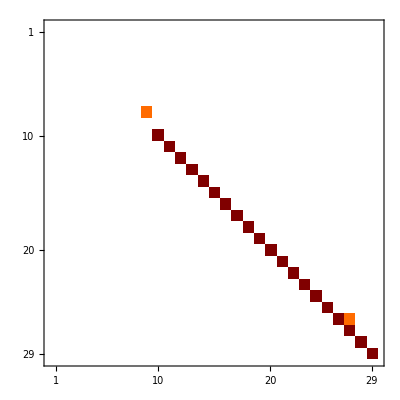

```mathematica
MatrixPlot[Factor@mt]
```

```mathematica
OptionValue
```

```mathematica
Sequence@@FilterRules[{Method->"CofactorExpansion"},Options[Inverse]]
```

Sequence[Method→CofactorExpansion]

```mathematica
Options[Inverse]
```

{Method→Automatic,Modulus→0,ZeroTest→Automatic}

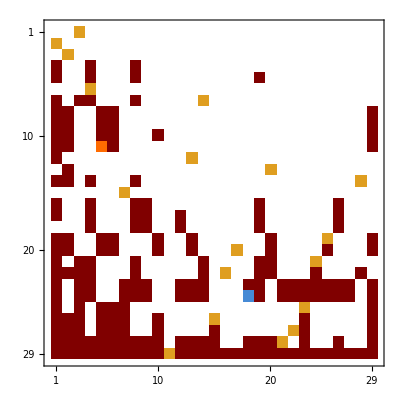

```mathematica
MatrixPlot[Transpose[InvertBT@t]]
```

```mathematica
FilterRules
```

```mathematica
Clear[JForm];
Options[JForm]={SimplifyFunction->Factor};
JForm[M_?SquareMatrixQ,opts:OptionsPattern[]]:=Module[{evs,mult,simplify,l=Length@m,mp},
simplify=OptionValue[SimplifyFunction];
{evs,mult}=Transpose@Tally[simplify@Eigenvalues[M]];
(*For each eigenvalue we calculate recursively the matrix rank of (m-λ)^k*)
Print[evs];
Map[Function[ev,mp=IdentityMatrix[l];Print@FixedPointList[(mp=simplify[mp.(m-ev)];MatrixRank[mp])&,l]],evs]
]
```

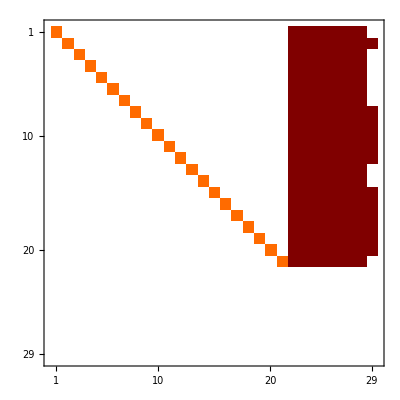

```mathematica
MatrixPlot[RowReduce[m]]
```

```mathematica
JForm[m]
```

{0,-3 ep,-5/2 (-1+2 ep),-3/2 (-1+2 ep),1/2 (1-2 ep),-1-3 ep,1/2 (1-8 ep),1-3 ep,1/2 (-1+2 ep),-ep}

{29,21,20,20}

{29,22,22}

{29,22,22}

{29,22,22}

«6 more identical outputs»

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
MatrixRank[m.m.m]
```

20

```mathematica
EntangledBlocksIndices[ds]
```

Read TClosure from extras.

{{1},{2},{3},{4,5,6},{7},{8,9,10,11},{12},{13},{14},{15},{16,17,18},{19,20},{21,22},{23,24},{25,26},{27},{28,29}}

```mathematica
ds[t]
```

```mathematica
ii={8,9,10,11}
```

{8,9,10,11}

```mathematica
ds[[ii,ii]]
```

<|s→{{(-2+5 ep)/((-4+s) s),-(-6+11 ep+ep s)/(2 (-1+2 ep) (-4+s) s),(ep (-1+3 ep))/(2 (-1+2 ep)^2),-(6-23 ep+22 ep^2-3 ep s+7 ep^2 s)/(2 (-1+2 ep)^2 (-4+s) s)},{-(2 (-1+2 ep) (-1+3 ep) (-3+s))/((-4+s) s),(5-11 ep-2 s+5 ep s)/((-4+s) s),-(ep (-1+3 ep))/(-1+2 ep),((-1+3 ep) (5-10 ep-2 s+5 ep s))/((-1+2 ep) (-4+s) s)},{-(4 (-1+2 ep)^2)/((-4+s) s),(3 (-1+2 ep))/((-4+s) s),-(-2-4 ep+5 ep s)/((-4+s) s),(-3+7 ep)/((-4+s) s)},{(2 (-1+2 ep)^2)/((-4+s) s),-(3 (-1+2 ep))/((-4+s) s),0,-(-3+2 ep+2 ep s)/((-4+s) s)}}|>

```mathematica
m=SeriesCoefficient[ds[s],{s,4,-1}];
```

```mathematica
t=JordanDecomposition[Transpose@m]
```

{{{-(2 (1-4 ep+4 ep^2))/(-2+5 ep),(2 (1-5 ep+6 ep^2))/(-2+5 ep),-(2 (-1+11 ep-32 ep^2+28 ep^3))/(ep (-3+5 ep)),-(2 (1-4 ep+4 ep^2))/(-3+10 ep)},{0,1,(6 (-1+2 ep))/(-3+5 ep),(3 (-1+2 ep))/(-3+10 ep)},{0,0,-(2 (1-13 ep+40 ep^2))/(ep (-3+5 ep)),0},{1,0,1,1}},{{0,0,0,0},{0,0,0,0},{0,0,1/2-4 ep,0},{0,0,0,-1/2+ep}}}

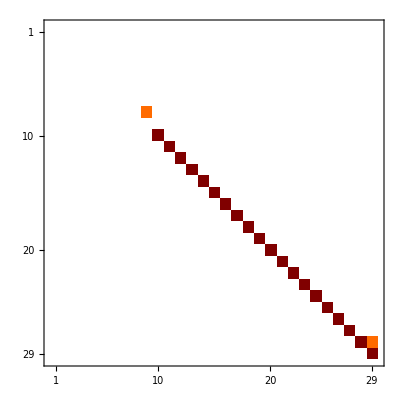

```mathematica
MatrixPlot[Last@%]
```

```mathematica
PolesInfo[ds[s],s]
```

{{0,2},{4,4},{∞,3}}

```mathematica
ii={52,53,54,55,59,60,61,62,70,71,72,73,74,75};
NewDEsystem[ss,ds[[ii,ii]]]
```

History length for ss is 1.

Successfully created differential system for 14 functions of s,t.

Next, you might want to find denominators appearing. See ?Denominators.

```mathematica
Timing[iss=InvertBT[ss[s]];]
```

{2.48,Null}

```mathematica
PolesInfo[ss[s],s]
```

{{0,2},{4,1},{1-t,3},{2-t,1},{(-1+2 t-t^2)/t,1},{(1-2 t ϵ)/ϵ,1},{∞,1}}

```mathematica
m=Factor@SeriesCoefficient[ss[s],{s,4,-1}];
```

```mathematica
Timing[{T,jf}=JordanDecomposition[m];]
```

{0.352,Null}

```mathematica
Factor[Transform[m,T]-jf]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

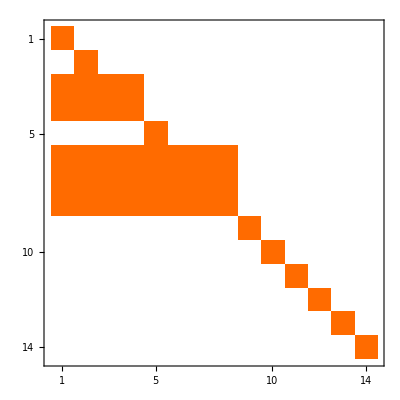

```mathematica
MatrixPlot@TClosure[m]
```

```mathematica
Adjugated
```

```mathematica
Timing[Inverse[ss[s],Method->"CofactorExpansion"]]
```

$Aborted

```mathematica
Denominators[ss]
```

Added extra(s) Denominators to current history entry.

{s,-1+t,t,-1+s+t,1-2 t+s t+t^2}

#### Fast Jordan form

https : // www - fourier.ujf - grenoble.fr/~parisse/publi/jordan.pdf

```mathematica
EntangledBlocksIndices[ds]
```

Read TClosure from extras.

{{1},{2},{3},{4},{5},{6},{7},{8},{9,10},{11},{12,13,14},{15},{16},{17},{18},{19},{20,21},{22},{23},{24},{25},{26},{27},{28},{29},{30,31},{32,33},{34,35},{36,37},{38,39},{40},{41},{42},{43},{44},{45,46},{47,48},{49},{50},{51},{52,53,54,55},{56},{57},{58},{59,60,61,62},{63},{64},{65},{66},{67},{68,69},{70,71,72},{73,74,75}}

```mathematica
ii={59,60,61,62};
NewDEsystem[ss,ds[[ii,ii]]];
```

History length for ss is 1.

Successfully created differential system for 4 functions of s,t.

Next, you might want to find denominators appearing. See ?Denominators.

```mathematica
pB[m_?SquareMatrixQ]:=Module[{a=m,n=Length@m,ps={},Bs={},p,B},
Append[Table[(a=DISY`Private`factorplus[B.a];#)&@{p=-Tr[a]/i,B=a+p IdentityMatrix[n]}
,{i,n-1}],{p=-Tr[a]/n,B=a+p IdentityMatrix[n]}]
]
```

```mathematica
Timing[InvertBT[ss[s]];]
```

{0.552,Null}

```mathematica
Timing[pB[ss[s]];]
```

{2.488,Null}

```mathematica
JordanDecomposition
```

## Real reduction

```mathematica
Select[EntangledBlocksIndices[ds],Length@#==4&]
```

Added extra(s) TClosure to current history entry.

{{52,53,54,55},{59,60,61,62}}

```mathematica
NewDEsystem[b,ds[[{52,53,54,55},{52,53,54,55}]]];
```

History length for b is 1.

Successfully created differential system for 4 functions of s,t.

Next, you might want to find denominators appearing. See ?Denominators.

```mathematica
ChangeVar[b,{s->(z-1) y/z,t->y/z+1},{y,z}];
```

History length for b is 2.

```mathematica
Factor[b];
```

History length for b is 3.

```mathematica
Denominators[b]
```

Read Denominators from extras.

{y,-1+z,z,-1+y+z,-y-4 z+y z,-z+y ϵ+2 z ϵ+y z ϵ}

```mathematica
ChangeVar[ds,{s->(z-1) (y)/z,t->y/z+1},{y,z}];
```

History length for ds is 2.

```mathematica
Factor[ds];
```

History length for ds is 3.

```mathematica
Denominators[ds]
```

Read Denominators from extras.

{-4+s,s,-2+t,-1+t,t,1+t,-3+s+t,-2+s+t,-1+s+t,s+t,1-2 t+s t+t^2,-1+s ϵ+2 t ϵ}

```mathematica
Denominators[b]
```

Read Denominators from extras.

{s,-1+t,-2+s+t,-1+s+t,1-2 t+s t+t^2}

```mathematica
HistoryIndex[b]
```

1

```mathematica
Undo[ds];
```

History length is 1.

```mathematica
EntangledBlocksIndices[ds]
```

Read TClosure from extras.

{{1},{2},{3},{4},{5},{6},{7},{8},{9,10},{11},{12,13,14},{15},{16},{17},{18},{19},{20,21},{22},{23},{24},{25},{26},{27},{28},{29},{30,31},{32,33},{34,35},{36,37},{38,39},{40},{41},{42},{43},{44},{45,46},{47,48},{49},{50},{51},{52,53,54,55},{56},{57},{58},{59,60,61,62},{63},{64},{65},{66},{67},{68,69},{70,71,72},{73,74,75}}